```mathematica
LozV[x_,y_,eps_]:={EdgeForm[Thickness[eps]],Darker[Gray],Polygon[{{x-1/2,y },{x-1/2,y +1},{x+1/2,y },{x+1/2,y-1},{x-1/2,y }}]}
```

```mathematica
LozV[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[70/256,162/256,141/256],Polygon[{{x-1/2,y },{x-1/2,y +1},{x+1/2,y },{x+1/2,y-1},{x-1/2,y }}]}
```

```mathematica
LozL[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[249/256,187/256,78/256],Polygon[{{x-1/2,y},{x-3/2,y+1 },{x-1/2,y+1},{x+1/2,y },{x-1/2,y }}]}
```

```mathematica
LozS[x_,y_,eps_]:={EdgeForm[Thickness[eps]],RGBColor[240/256,92/256,80/256],Polygon[{{x-1/2,y},{x-1/2,y+1},{x+1/2,y+1},{x+1/2,y },{x-1/2,y }}]}
```

```mathematica
FF[x_,k_]:=Sum[If[x>=λ[[1]][[k]][[i]]-i,1,0],{i,1,k}]-If[k>1,Sum[If[x>=λ[[1]][[k-1]][[i]]-i,1,0],{i,1,k-1}],0]
```

```mathematica
eps:=0.00015
```

```mathematica
t:={{1,1/2},{0,.85}}
```

```mathematica
Do[
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];n=Length[λ[[1]]];Export[ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/agg``.png",a+10]],Graphics[GeometricTransformation[{{Table[If[FF[x,k]==1,LozS[x+1,k-1,eps],If[x+k>0,LozL[x+1,k-1,eps]]],{k,1,n},{x,-n+1,n/2-1}],Table[LozV[λ[[1]][[i]][[j]]-j,i,eps],{i,1,n},{j,1,i}]},Line[{{1,0},{n/2+1/2,0},{n/2+1/2,0}+n/2{0,1},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0}+{0,-n/2},{n/2+1/2,0}+n/2{0,1}+{-n/2,n/2}+{-n/2,0}+{0,-n/2}+{n/2,-n/2}}]},t]],ImageResolution->500],{a,824,824}]
```

```mathematica
e
```

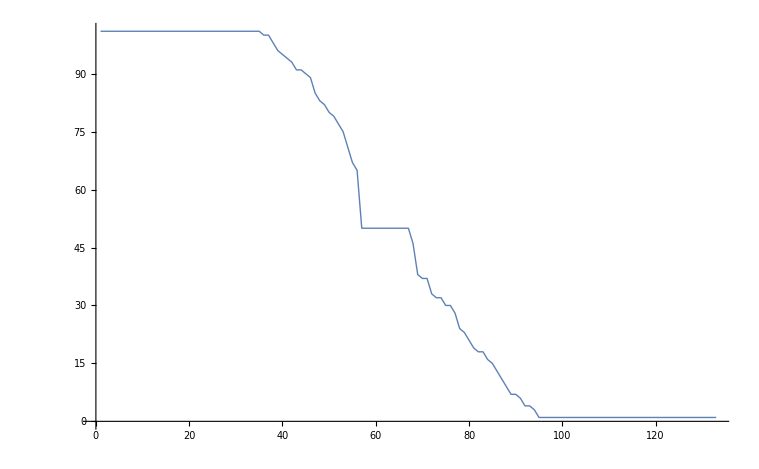

```mathematica
ListLinePlot[Table[λ[[1]][[Floor[2n/3]]][[i]],{i,1,2n/3}],PlotRange->Full,PlotStyle->Thick,PlotRange->Full]
```

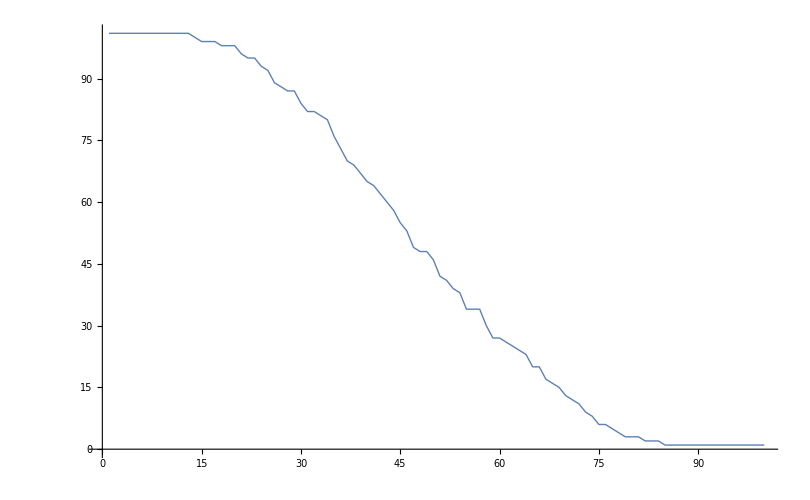

```mathematica
ListLinePlot[Table[λ[[1]][[Floor[n/2]]][[i]],{i,1,n/2}],PlotRange->Full,PlotStyle->Thick,PlotRange->Full]
```

```mathematica
avg:=Table[0,{i,1,2n/3}];count:=0
```

```mathematica
Do[
fileName=ToString[StringForm["/Users/leo/Dropbox/Sci/Glauber_Simulation/output``.txt",a]];λ=ReadList[fileName];avg+=Table[λ[[1]][[Floor[2n/3]]][[i]],{i,1,2n/3}];count+=1,{a,500,824}]
```

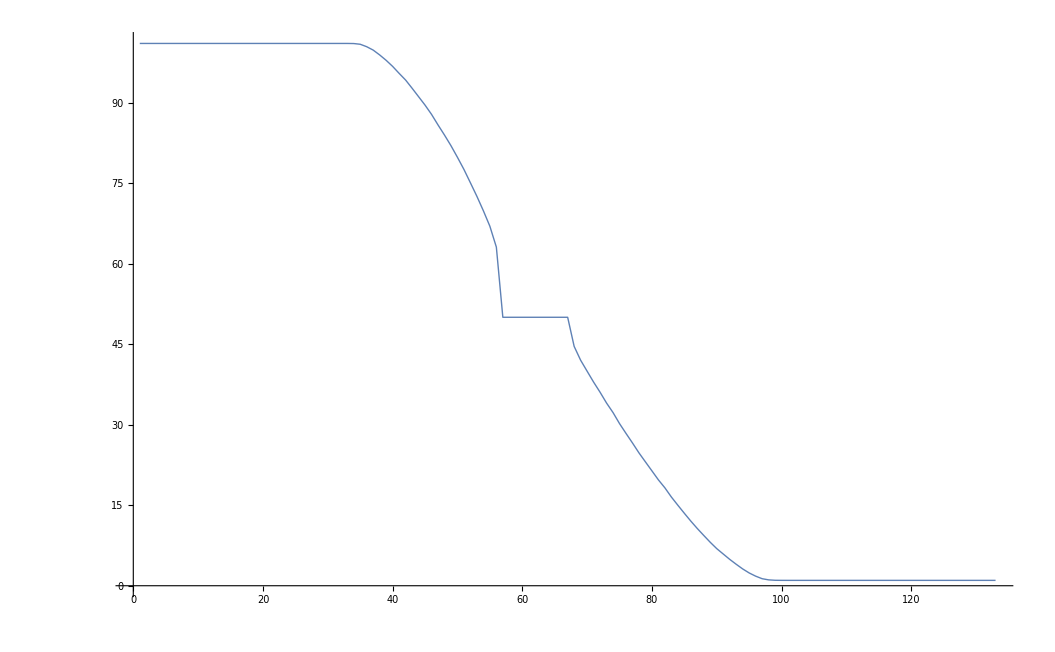

```mathematica
ListLinePlot[avg/count,PlotStyle->Thick]
```

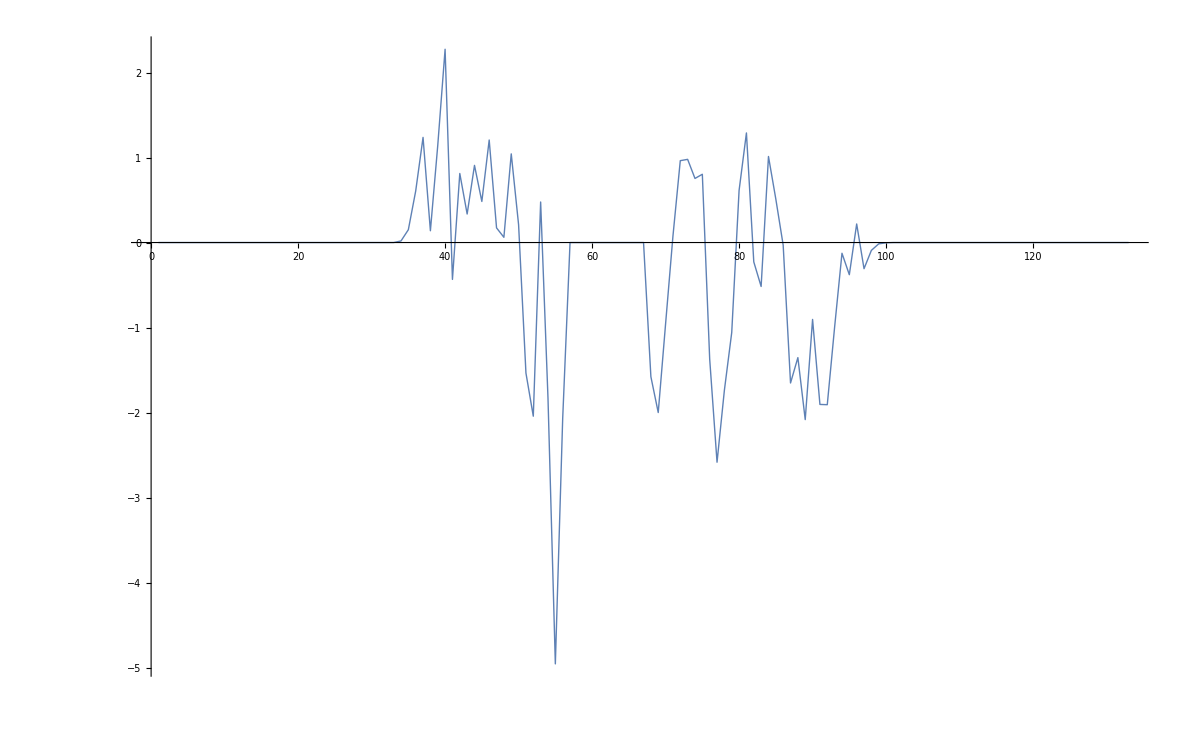

```mathematica
ListLinePlot[Table[λ[[1]][[Floor[2n/3]]][[i]],{i,1,2n/3}]-avg/count,PlotRange->Full,PlotStyle->Thick]
```